## Tutorial: Flat-bands, hyperbolic kagome lattice

This is a notebook for the first steps for the use of the HyperBloch package for efficient modeling of tight-binding models on hyperbolic lattices.

## Preliminaries:

### Remark:

Before using the getting started with the HyperBloch notebook:

Make sure that the HyperBloch package is installed, if this is not the case please follow the instruction on the website (link to website ???).

Make sure that the required files .hcc,  .hcm and .hcs files are in the current directory. This entails files:

(2,3,8)_T2.1_3.hcc

{8,3}-kagome_T2.1_3.hcm

{8,3}-kagome_T2.1_3_sc-T5.1.hcs

{8,3}-kagome_T2.1_3_sc-T17.2.hcs

In case no such files exists, please follow the instructions in the the prerequisites section on the website (link to website ???) or download it there.

### Load the HyperBloch package:

```mathematica
<<PatrickMLenggenhager`HyperBloch`
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

Open the documentation:

```mathematica
Documentation`HelpLookup["PatrickMLenggenhager/HyperBloch/tutorial/BasicUsage"];
```

```mathematica
Documentation`HelpLookup["PatrickMLenggenhager/HyperBloch/guide/HyperBlochPackage"];
```

### Needed functions:

```mathematica
ComputeEigenvalues[cfH_,Npts_,Nruns_,genus_]:=
Flatten@ParallelTable[
Flatten@Table[
Eigenvalues[cfH@@RandomReal[{-Pi,Pi},2genus]],{i,1,Round[Npts/Nruns]}],
{j,1,Nruns},Method->"FinestGrained"]
```

## {8,3} kagome lattice:

### Import cells

We first import the cell, model, and supercell model graphs as produced by the HyperCells package:

We consider the following sequence of supercells, defined in terms of quotients given in https://www.math.auckland.ac.nz/~conder/TriangleGroupQuotients101.txt by M. Conder, (the cell “T2.6” is the primitive cell):

```mathematica
cellsKagome={"T2.1","T5.1","T17.2"}; 
genusLstKagome={2,5,17};
```

Cell graph:

```mathematica
pcellKagome=ImportCellGraphString[Import["(2,3,8)_T2.1_3.hcc"]];
```

Primitive cell:

```mathematica
pcmodelKagome=ImportModelGraphString[Import["{8,3}-kagome_T2.1_3.hcm"]];
```

Visualize the model graph:

```mathematica
VisualizeModelGraph[pcmodelKagome,
Elements-><|
			ShowCellGraphFlattened->{},
			ShowCellBoundary->{ShowEdgeIdentification->True}
		|>,

CellGraph->pcellKagome,
NumberOfGenerations->3,
ImageSize->400]
```

-Graphics-

We proceed by computing the density of states. Since the computations for supercells larger than supercell T5.1 are time consuming, we split this section into two parts. The DOS for supercell T17.2 will take a lot more time to compute than the first part.

### Computations up to 1st supercell:

Supercells:

The Hamiltonians for the nearest - neighbor tight - binding model on the sequence of supercells are, (this might take a minute):

```mathematica
scmodelsKagome=Association[cellsKagome[[2]]->
ImportSupercellModelGraphString[ 
Import[ToString@StringForm["{8,3}-kagome_T2.1_3_sc-``.hcs",cellsKagome[[2]]]]]];
```

#### Hamiltonian :

Primitive cell:

The Hamiltonian for the nearest-neighbor tight-binding model on the primitive cell T2.1 is:

```mathematica
HpcKagome=AbelianBlochHamiltonian[pcmodelKagome,1,0&,-1&,CompileFunction->True];
```

Supercells:

The Hamiltonians for the nearest - neighbor tight - binding model on the sequence of supercells are, (this might takes a  minutes):

```mathematica
HclstKagome=
Join[Association["T2.1"->HpcKagome],
Association[cellsKagome[[2]]->
AbelianBlochHamiltonian[scmodelsKagome["T5.1"],1,0&,-1&,PCModel->pcmodelKagome,CompileFunction->True]]];
```

#### Density of states:

Let us compute the density of states by exact diagonalization.

Compute the Eigenvalues via 2·10^4 momentum random samples, (this might take a minute):

```mathematica
evalsKagome1=Association[cellsKagome[[#]]->ComputeEigenvalues[HclstKagome[cellsKagome[[#]]],2 10^4,32,genusLstKagome[[#]]]&/@Range[2]];
```

Visualize density of states via a kernel density estimation, (this might take a minute):

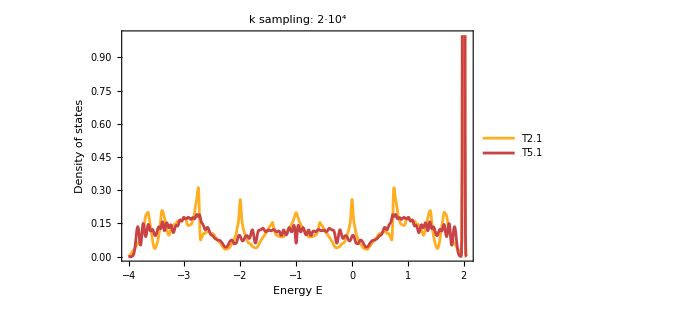

```mathematica
SmoothHistogram[evalsKagome1,0.01,"PDF",Frame->True,FrameStyle->Black,FrameLabel->{"Energy E","Density of states"},PlotRange->{0,1}, LabelStyle->20,PlotLabel->"k sampling: 2·10^4",PlotStyle->(ColorData["SunsetColors","ColorFunction"]/@(1-Range[1,3]/3.)),ImageSize->500,ImagePadding->{{Automatic, 10}, {Automatic, 10}},Background->None]
```

### Computations up to 2nd supercell:

Supercells:

The Hamiltonians for the nearest - neighbor tight - binding model on the sequence of supercells are, (this might take a minute):

```mathematica
scmodelsKagome2=Association[cellsKagome[[3]]->
ImportSupercellModelGraphString[ 
Import[ToString@StringForm["{8,3}-kagome_T2.1_3_sc-``.hcs",cellsKagome[[3]]]]]];
```

#### Hamiltonian :

Supercells:

The Hamiltonians for the nearest - neighbor tight - binding model on the sequence of supercells are, (this might take a few minutes):

```mathematica
HclstKagome2=
Association[cellsKagome[[3]]->
AbelianBlochHamiltonian[scmodelsKagome2["T17.2"],1,0&,-1&,PCModel->pcmodelKagome,CompileFunction->True]];
```

#### Density of states:

Let us compute the density of states by exact diagonalization.

Compute the Eigenvalues via 2 · 10^4 momentum random samples, (Caution, this takes a long time to compute):

```mathematica
evalsKagome2=Association[cellsKagome[[3]]->ComputeEigenvalues[HclstKagome2[cellsKagome[[3]]],2 10^4,32,genusLstKagome[[3]]]];
```

Visualize density of states via a kernel density estimation, (this might take a few minutes):

```mathematica
evalsKagome=Join[evalsKagome1,evalsKagome2];
```

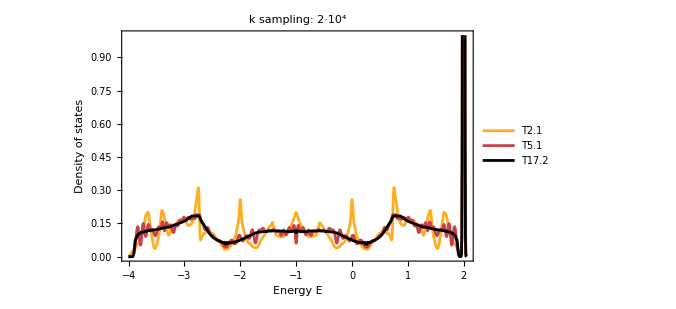

```mathematica
SmoothHistogram[evalsKagome,0.01,"PDF",Frame->True,FrameStyle->Black,FrameLabel->{"Energy E","Density of states"},PlotRange->{0,1}, LabelStyle->20,PlotLabel->"k sampling: 2·10^4",PlotStyle->(ColorData["SunsetColors","ColorFunction"]/@(1-Range[1,3]/3.)),ImageSize->500,ImagePadding->{{Automatic, 10}, {Automatic, 10}},Background->None]
```

```mathematica
NotebookSave[]
```